### 基本閉路行列の関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
Pin={{0,0},{1,2},{1.5,0.5},{3,0.7},{3.5,3.3},{5,0}}(*Point input*)
```

{{0,0},{1,2},{1.5,0.5},{3,0.7},{3.5,3.3},{5,0}}

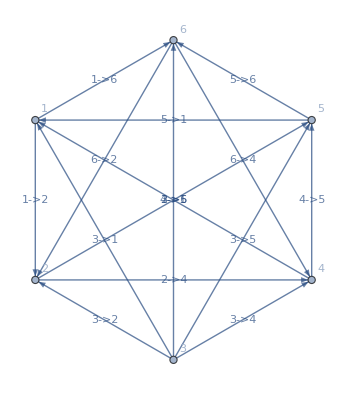

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Random"](*Ggraph input*)
```

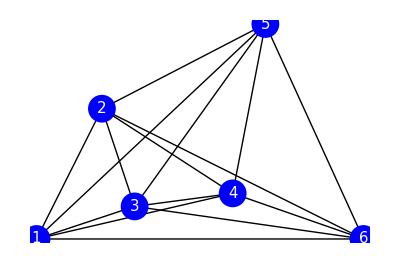

```mathematica
Graphics[{Thick,Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]
}]
```

```mathematica
h=LoopMatrix[Gin]
```

{{0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,1},{0,0,-1,1,0,0,0,0,0,0,0,0,1,0,0},{0,0,-1,0,-1,0,0,0,0,0,0,0,0,-1,0},{0,-1,0,0,-1,0,0,0,0,0,0,1,0,0,0},{0,-1,0,1,0,0,0,0,0,0,1,0,0,0,0},{0,-1,1,0,0,0,0,0,0,1,0,0,0,0,0},{1,0,0,1,0,0,0,1,0,0,0,0,0,0,0},{1,0,1,0,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,-1,0,0,0,-1,0,0,0,0,0,0},{1,1,0,0,0,-1,0,0,0,0,0,0,0,0,0}}

```mathematica
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}](* Point Distance *)
```

{√5,1.58114,3.08058,4.81041,5,1.58114,2.38537,2.8178,2 √5,1.51327,3.44093,3.53553,2.64764,2.11896,3.62491}

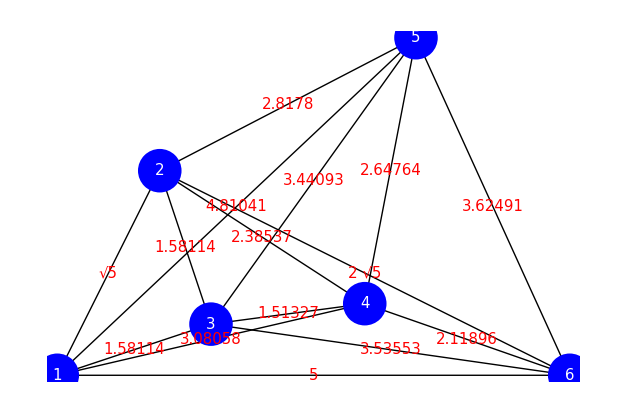

```mathematica
Graphics[{Thick,Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[PD[[i]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}]
```

```mathematica
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD
```

{{√5,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,1.58114,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,3.08058,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,4.81041,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0,0,0,0,5,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,1.58114,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.38537,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.8178,0.,0.,0.,0.,0.,0.,0.},{0,0,0,0,0,0,0,0,2 √5,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.51327,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.44093,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.53553,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.64764,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.11896,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.62491}}

```mathematica
s=Table[0,{i,Length[EdgeRules[Gin]]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FLP=Table[
Pin[[
ConnectedComponents[FundLoop[[i]]][[1]]
]],
{i,Length[FundLoop]}](* Fundamental Loop Point *)
```

{{{5,0},{0,0},{3.5,3.3}},{{3.5,3.3},{0,0},{3,0.7}},{{5,0},{0,0},{3,0.7}},{{5,0},{0,0},{1.5,0.5}},{{3.5,3.3},{0,0},{1.5,0.5}},{{3,0.7},{0,0},{1.5,0.5}},{{3.5,3.3},{0,0},{1,2}},{{3,0.7},{0,0},{1,2}},{{5,0},{0,0},{1,2}},{{1.5,0.5},{0,0},{1,2}}}

```mathematica
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}<0,1,-1],
{i,Length[FundLoop]}](* 右回りならば正、左回りならば負 *)
```

{1,-1,1,1,-1,1,1,1,1,1}

```mathematica
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[FundLoop[[i]]][[1]]]]
]],
{i,Length[FundLoop]}](* Fundamental Loop Area *)
```

{8.25,3.725,1.75,1.25,1.6,0.225,1.85,2.65,5,1.25}

```mathematica
U=Table[-LoopSpin[[i]]FLA[[i]],{i,Length[FundLoop]}](* 誘導起電力行列(誘導起電力は-B'Sに右回りなら1を、左回りなら-1をかける) *)
```

{-8.25,3.725,-1.75,-1.25,1.6,-0.225,-1.85,-2.65,-5,-1.25}

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{-0.671869,-0.176089,-0.298125,0.385242,0.582897,-0.335685,-0.0961094,-0.781044,0.130401,0.274226,-0.15449,0.392038,0.360106,-0.116135,-0.96067}

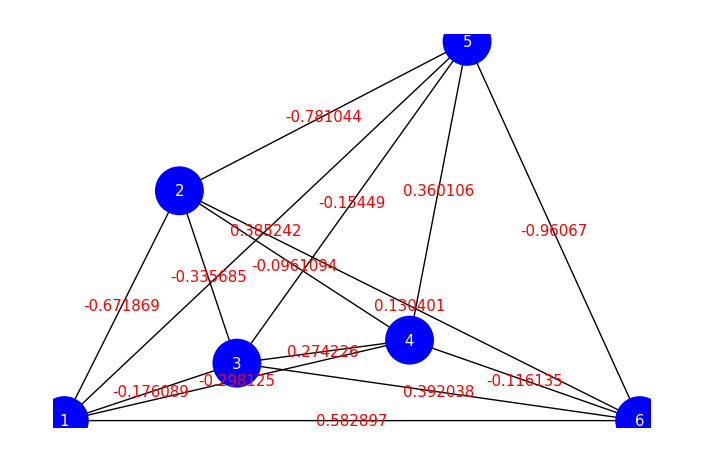

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[Curr[[i]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}]
```

```mathematica
Sort[Abs[Curr],Greater]
```

{0.96067,0.781044,0.671869,0.582897,0.392038,0.385242,0.360106,0.335685,0.298125,0.274226,0.176089,0.15449,0.130401,0.116135,0.0961094}

```mathematica
FindShortestTour[Pin]
```

{13.8922,{1,3,4,6,5,2,1}}

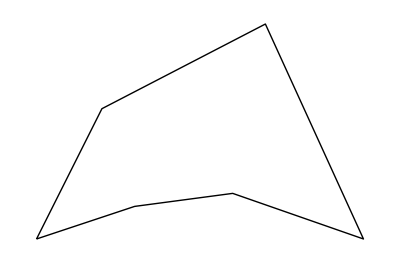

```mathematica
Graphics[Line[Pin[[Last[%]]]]]
```

```mathematica
ArrowList=Arrow[Table[If[Curr[[i]]>0,
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]}
],{i,Length[EdgeRules[Gin]]}
]]
```

Arrow[{{{1,2},{0,0}},{{0,0},{1.5,0.5}},{{0,0},{3,0.7}},{{3.5,3.3},{0,0}},{{0,0},{5,0}},{{1,2},{1.5,0.5}},{{3,0.7},{1,2}},{{3.5,3.3},{1,2}},{{5,0},{1,2}},{{1.5,0.5},{3,0.7}},{{3.5,3.3},{1.5,0.5}},{{1.5,0.5},{5,0}},{{3,0.7},{3.5,3.3}},{{3,0.7},{5,0}},{{5,0},{3.5,3.3}}}]

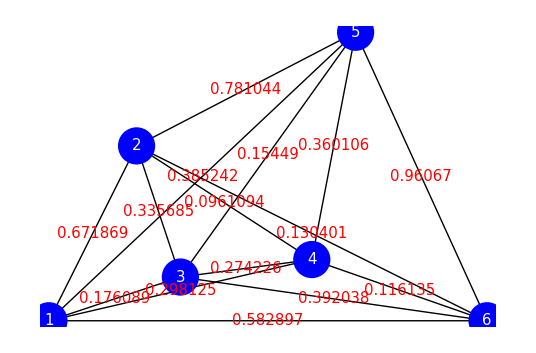

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],ArrowList,
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[Abs[Curr[[i]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}]
```